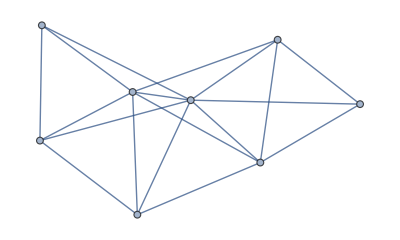
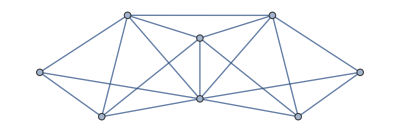
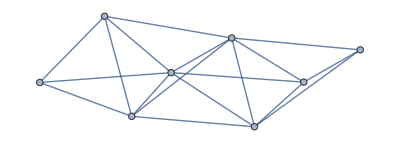
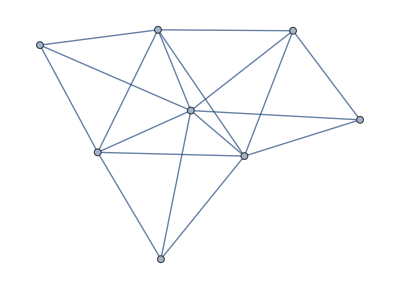
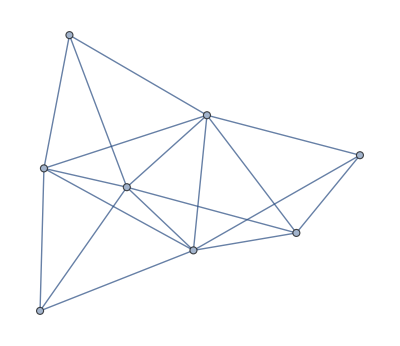
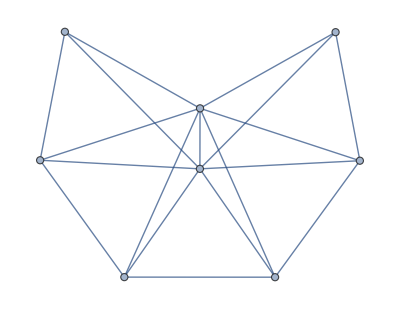
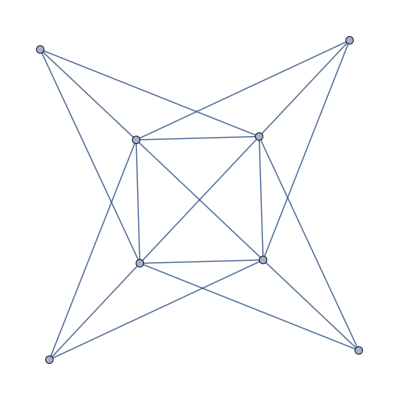

```mathematica
gr=Select[Map[Graph,ReadPlantri["D:\\cygwin64\\home\\alfre\\plantri8.txt"]],ChromaticPolynomial[#,4]==24&&PlanarGraphQ[#]&]
```

```mathematica
TableForm[Map[Map [Last,#]&,Map[FormulaLevels[FindFullFormula[#]]&,gr]],TableDepth->2]
```

1 | 15 | 25 | 10 | 1
1 | 15 | 25 | 10 | 1
1 | 15 | 25 | 10 | 1
1 | 15 | 25 | 10 | 1
1 | 15 | 25 | 10 | 1
1 | 15 | 25 | 10 | 1
1 | 15 | 25 | 10 | 1

```mathematica
TableForm[Map[GatherBy[FindFullFormula[#],SymbolLevel[#]&]&,gr],TableDepth->3]
```

{v1x2x3x4x5x6x7x8} | {v1x2x3x4x5x68x7}
{v1x2x3x4x58x6x7}
{v1x2x3x4x57x6x8}
{v1x2x3x48x5x6x7}
{v1x2x3x47x5x6x8}
{v1x2x3x46x5x7x8}
{v1x2x38x4x5x6x7}
{v1x26x3x4x5x7x8}
{v1x25x3x4x6x7x8}
{v1x24x3x5x6x7x8} | {v1x2x3x4x57x68}
{v1x2x3x48x57x6}
{v1x2x3x47x5x68}
{v1x2x3x47x58x6}
{v1x2x3x468x5x7}
{v1x2x3x46x58x7}
{v1x2x3x46x57x8}
{v1x2x38x4x57x6}
{v1x2x38x47x5x6}
{v1x2x38x46x5x7}
{v1x26x3x4x58x7}
{v1x26x3x4x57x8}
{v1x26x3x48x5x7}
{v1x26x3x47x5x8}
{v1x26x38x4x5x7}
{v1x25x3x4x68x7}
{v1x25x3x48x6x7}
{v1x25x3x47x6x8}
{v1x25x3x46x7x8}
{v1x25x38x4x6x7}
{v1x246x3x5x7x8}
{v1x24x3x5x68x7}
{v1x24x3x58x6x7}
{v1x24x3x57x6x8}
{v1x24x38x5x6x7} | {v1x2x3x468x57}
{v1x2x38x46x57}
{v1x26x3x48x57}
{v1x26x3x47x58}
{v1x26x38x4x57}
{v1x26x38x47x5}
{v1x25x3x47x68}
{v1x25x3x468x7}
{v1x25x38x47x6}
{v1x25x38x46x7}
{v1x246x3x58x7}
{v1x246x3x57x8}
{v1x24x3x57x68}
{v1x246x38x5x7}
{v1x24x38x57x6} | {v1x246x38x57}
{v1x2x3x4x5x6x7x8} | {v1x2x3x4x5x68x7}
{v1x2x3x47x5x6x8}
{v1x2x3x46x5x7x8}
{v1x2x38x4x5x6x7}
{v1x2x37x4x5x6x8}
{v1x2x36x4x5x7x8}
{v1x2x35x4x6x7x8}
{v1x27x3x4x5x6x8}
{v1x26x3x4x5x7x8}
{v1x25x3x4x6x7x8} | {v1x2x3x47x5x68}
{v1x2x38x47x5x6}
{v1x2x38x46x5x7}
{v1x2x37x4x5x68}
{v1x2x37x46x5x8}
{v1x2x368x4x5x7}
{v1x2x36x47x5x8}
{v1x2x35x4x68x7}
{v1x2x35x47x6x8}
{v1x2x35x46x7x8}
{v1x27x3x4x5x68}
{v1x27x3x46x5x8}
{v1x27x38x4x5x6}
{v1x27x36x4x5x8}
{v1x27x35x4x6x8}
{v1x26x3x47x5x8}
{v1x26x38x4x5x7}
{v1x26x37x4x5x8}
{v1x26x35x4x7x8}
{v1x25x3x4x68x7}
{v1x25x3x47x6x8}
{v1x25x3x46x7x8}
{v1x25x38x4x6x7}
{v1x25x37x4x6x8}
{v1x25x36x4x7x8} | {v1x2x368x47x5}
{v1x2x35x47x68}
{v1x27x38x46x5}
{v1x27x368x4x5}
{v1x27x35x4x68}
{v1x27x35x46x8}
{v1x26x38x47x5}
{v1x26x35x47x8}
{v1x25x3x47x68}
{v1x25x38x47x6}
{v1x25x38x46x7}
{v1x25x37x4x68}
{v1x25x37x46x8}
{v1x25x368x4x7}
{v1x25x36x47x8} | {v1x25x368x47}
{v1x2x3x4x5x6x7x8} | {v1x2x3x4x58x6x7}
{v1x2x3x4x57x6x8}
{v1x2x3x48x5x6x7}
{v1x2x3x47x5x6x8}
{v1x2x3x46x5x7x8}
{v1x2x38x4x5x6x7}
{v1x2x37x4x5x6x8}
{v1x25x3x4x6x7x8}
{v1x24x3x5x6x7x8}
{v18x2x3x4x5x6x7} | {v1x2x3x48x57x6}
{v1x2x3x47x58x6}
{v1x2x3x46x58x7}
{v1x2x3x46x57x8}
{v1x2x38x4x57x6}
{v1x2x38x47x5x6}
{v1x2x38x46x5x7}
{v1x2x37x4x58x6}
{v1x2x37x48x5x6}
{v1x2x37x46x5x8}
{v1x25x3x48x6x7}
{v1x25x3x47x6x8}
{v1x25x3x46x7x8}
{v1x25x38x4x6x7}
{v1x25x37x4x6x8}
{v1x24x3x58x6x7}
{v1x24x3x57x6x8}
{v1x24x38x5x6x7}
{v1x24x37x5x6x8}
{v18x2x3x4x57x6}
{v18x2x3x47x5x6}
{v18x2x3x46x5x7}
{v18x2x37x4x5x6}
{v18x25x3x4x6x7}
{v18x24x3x5x6x7} | {v1x2x38x46x57}
{v1x2x37x46x58}
{v1x25x38x47x6}
{v1x25x38x46x7}
{v1x25x37x48x6}
{v1x25x37x46x8}
{v1x24x38x57x6}
{v1x24x37x58x6}
{v18x2x3x46x57}
{v18x2x37x46x5}
{v18x25x3x47x6}
{v18x25x3x46x7}
{v18x25x37x4x6}
{v18x24x3x57x6}
{v18x24x37x5x6} | {v18x25x37x46}
{v1x2x3x4x5x6x7x8} | {v1x2x3x4x5x68x7}
{v1x2x3x4x58x6x7}
{v1x2x3x48x5x6x7}
{v1x2x3x47x5x6x8}
{v1x2x3x46x5x7x8}
{v1x2x38x4x5x6x7}
{v1x2x36x4x5x7x8}
{v1x26x3x4x5x7x8}
{v1x25x3x4x6x7x8}
{v1x24x3x5x6x7x8} | {v1x2x3x47x5x68}
{v1x2x3x47x58x6}
{v1x2x3x468x5x7}
{v1x2x3x46x58x7}
{v1x2x38x47x5x6}
{v1x2x38x46x5x7}
{v1x2x368x4x5x7}
{v1x2x36x4x58x7}
{v1x2x36x48x5x7}
{v1x2x36x47x5x8}
{v1x26x3x4x58x7}
{v1x26x3x48x5x7}
{v1x26x3x47x5x8}
{v1x26x38x4x5x7}
{v1x25x3x4x68x7}
{v1x25x3x48x6x7}
{v1x25x3x47x6x8}
{v1x25x3x46x7x8}
{v1x25x38x4x6x7}
{v1x25x36x4x7x8}
{v1x246x3x5x7x8}
{v1x24x3x5x68x7}
{v1x24x3x58x6x7}
{v1x24x38x5x6x7}
{v1x24x36x5x7x8} | {v1x2x368x47x5}
{v1x2x36x47x58}
{v1x26x3x47x58}
{v1x26x38x47x5}
{v1x25x3x47x68}
{v1x25x3x468x7}
{v1x25x38x47x6}
{v1x25x38x46x7}
{v1x25x368x4x7}
{v1x25x36x48x7}
{v1x25x36x47x8}
{v1x246x3x58x7}
{v1x246x38x5x7}
{v1x24x368x5x7}
{v1x24x36x58x7} | {v1x25x368x47}
{v1x2x3x4x5x6x7x8} | {v1x2x3x4x5x6x78}
{v1x2x3x4x57x6x8}
{v1x2x3x48x5x6x7}
{v1x2x3x47x5x6x8}
{v1x2x3x46x5x7x8}
{v1x2x37x4x5x6x8}
{v1x28x3x4x5x6x7}
{v1x25x3x4x6x7x8}
{v1x24x3x5x6x7x8}
{v18x2x3x4x5x6x7} | {v1x2x3x48x57x6}
{v1x2x3x478x5x6}
{v1x2x3x46x5x78}
{v1x2x3x46x57x8}
{v1x2x37x48x5x6}
{v1x2x37x46x5x8}
{v1x28x3x4x57x6}
{v1x28x3x47x5x6}
{v1x28x3x46x5x7}
{v1x28x37x4x5x6}
{v1x25x3x4x6x78}
{v1x25x3x48x6x7}
{v1x25x3x47x6x8}
{v1x25x3x46x7x8}
{v1x25x37x4x6x8}
{v1x248x3x5x6x7}
{v1x24x3x5x6x78}
{v1x24x3x57x6x8}
{v1x24x37x5x6x8}
{v18x2x3x4x57x6}
{v18x2x3x47x5x6}
{v18x2x3x46x5x7}
{v18x2x37x4x5x6}
{v18x25x3x4x6x7}
{v18x24x3x5x6x7} | {v1x28x3x46x57}
{v1x28x37x46x5}
{v1x25x3x478x6}
{v1x25x3x46x78}
{v1x25x37x48x6}
{v1x25x37x46x8}
{v1x248x3x57x6}
{v1x248x37x5x6}
{v18x2x3x46x57}
{v18x2x37x46x5}
{v18x25x3x47x6}
{v18x25x3x46x7}
{v18x25x37x4x6}
{v18x24x3x57x6}
{v18x24x37x5x6} | {v18x25x37x46}
{v1x2x3x4x5x6x7x8} | {v1x2x3x4x5x68x7}
{v1x2x3x48x5x6x7}
{v1x2x3x47x5x6x8}
{v1x2x3x46x5x7x8}
{v1x2x38x4x5x6x7}
{v1x2x37x4x5x6x8}
{v1x2x36x4x5x7x8}
{v1x27x3x4x5x6x8}
{v1x26x3x4x5x7x8}
{v1x24x3x5x6x7x8} | {v1x2x3x47x5x68}
{v1x2x3x468x5x7}
{v1x2x38x47x5x6}
{v1x2x38x46x5x7}
{v1x2x37x4x5x68}
{v1x2x37x48x5x6}
{v1x2x37x46x5x8}
{v1x2x368x4x5x7}
{v1x2x36x48x5x7}
{v1x2x36x47x5x8}
{v1x27x3x4x5x68}
{v1x27x3x48x5x6}
{v1x27x3x46x5x8}
{v1x27x38x4x5x6}
{v1x27x36x4x5x8}
{v1x26x3x48x5x7}
{v1x26x3x47x5x8}
{v1x26x38x4x5x7}
{v1x26x37x4x5x8}
{v1x247x3x5x6x8}
{v1x246x3x5x7x8}
{v1x24x3x5x68x7}
{v1x24x38x5x6x7}
{v1x24x37x5x6x8}
{v1x24x36x5x7x8} | {v1x2x37x468x5}
{v1x2x368x47x5}
{v1x27x3x468x5}
{v1x27x38x46x5}
{v1x27x368x4x5}
{v1x27x36x48x5}
{v1x26x38x47x5}
{v1x26x37x48x5}
{v1x247x3x5x68}
{v1x247x38x5x6}
{v1x246x38x5x7}
{v1x246x37x5x8}
{v1x24x37x5x68}
{v1x24x368x5x7}
{v1x247x36x5x8} | {v1x247x368x5}
{v1x2x3x4x5x6x7x8} | {v1x2x3x4x5x6x78}
{v1x2x3x4x58x6x7}
{v1x2x3x4x57x6x8}
{v1x2x3x47x5x6x8}
{v1x2x38x4x5x6x7}
{v1x2x37x4x5x6x8}
{v1x2x36x4x5x7x8}
{v1x2x35x4x6x7x8}
{v1x25x3x4x6x7x8}
{v18x2x3x4x5x6x7} | {v1x2x3x4x578x6}
{v1x2x3x47x58x6}
{v1x2x38x4x57x6}
{v1x2x38x47x5x6}
{v1x2x378x4x5x6}
{v1x2x37x4x58x6}
{v1x2x36x4x5x78}
{v1x2x36x4x58x7}
{v1x2x36x4x57x8}
{v1x2x36x47x5x8}
{v1x2x358x4x6x7}
{v1x2x357x4x6x8}
{v1x2x35x4x6x78}
{v1x2x35x47x6x8}
{v1x25x3x4x6x78}
{v1x25x3x47x6x8}
{v1x25x38x4x6x7}
{v1x25x37x4x6x8}
{v1x25x36x4x7x8}
{v18x2x3x4x57x6}
{v18x2x3x47x5x6}
{v18x2x37x4x5x6}
{v18x2x36x4x5x7}
{v18x2x35x4x6x7}
{v18x25x3x4x6x7} | {v1x2x36x4x578}
{v1x2x36x47x58}
{v1x2x3578x4x6}
{v1x2x358x47x6}
{v1x25x38x47x6}
{v1x25x378x4x6}
{v1x25x36x4x78}
{v1x25x36x47x8}
{v18x2x36x4x57}
{v18x2x36x47x5}
{v18x2x357x4x6}
{v18x2x35x47x6}
{v18x25x3x47x6}
{v18x25x37x4x6}
{v18x25x36x4x7} | {v18x25x36x47}

## Now let' s paint the mobius graph

```mathematica
FormulaGraphReverse3[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s2]-> SetsToSymbol[s1]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> Rotate[SymbolToLabel2[SetsToSymbol2[ s]],Pi/4],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
Inrecurse[g_,v_]:=Block[{todo={v},done={},result={},current,g2,v2},
While[todo≠{},
current=First[todo];
todo=Rest[todo];
AppendTo[done,current];
g2=NeighborhoodGraph[g,current];
Table[
v2=e[[1]];
If[!MemberQ[done,v2],
AppendTo[todo,v2];
If[!MemberQ[result,e],
AppendTo[result,e]
]
]
,{e,EdgeList[g2]}
]
];
result
]
```

```mathematica
HighGr[g_]:=With[
{last=First[Select[VertexList[g],VertexOutDegree[g,#]==0&&SymbolLevel[#]==4&]]},
Inrecurse[g,last]
]
```

```mathematica
Table[
g->FormulaLevels[VertexList[HighGr[FormulaGraphReverse3[FindFullFormula[ g]]]]]
,{g,gr}]
```

{-Graphics-→{{4,1},{5,5},{6,8},{7,5},{8,1}},-Graphics-→{{4,1},{5,5},{6,8},{7,5},{8,1}},-Graphics-→{{4,1},{5,4},{6,6},{7,4},{8,1}},-Graphics-→{{4,1},{5,5},{6,8},{7,5},{8,1}},-Graphics-→{{4,1},{5,4},{6,6},{7,4},{8,1}},-Graphics-→{{4,1},{5,6},{6,11},{7,6},{8,1}},-Graphics-→{{4,1},{5,4},{6,6},{7,4},{8,1}}}

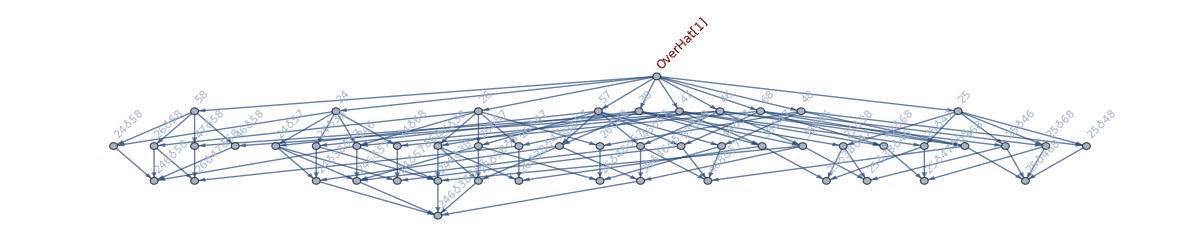
-Graphics-{{4,1},{5,5},{6,8},{7,5},{8,1}}

```mathematica
With[
{g=FormulaGraphReverse3[FindFullFormula[ gr[[1]]]]},
Labeled[Graph[g,ImageSize-> {1200,Automatic},GraphHighlight->HighGr[g]],FormulaLevels[VertexList[HighGr[g]]]]
]
```